```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

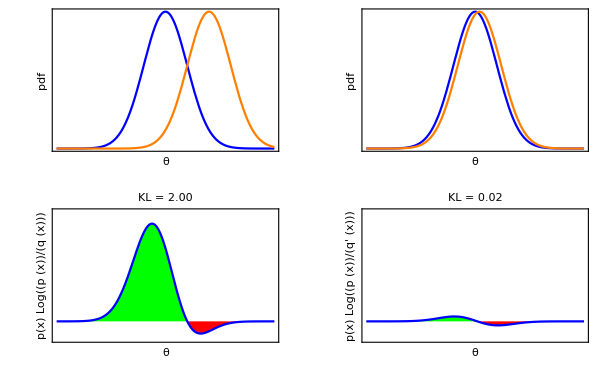

```mathematica
aDist  = NormalDistribution[5,1];
bDist = NormalDistribution[7,1];
cDist = NormalDistribution[5.2,1];
klYRange = {-0.2,1.2};
kl1 = NIntegrate[PDF[aDist,x]*Log[PDF[aDist,x]/PDF[bDist,x]],{x,0,10}];
kl2 = NIntegrate[PDF[aDist,x]*Log[PDF[aDist,x]/PDF[cDist,x]],{x,0,10}];
g1=Plot[{PDF[aDist,x],PDF[bDist,x]},{x,0,10},Axes->None,Frame->{True,True,False,False},PlotStyle->{Blue,Orange},FrameTicks->{None,None},FrameLabel->{"θ","pdf\n\n"},BaseStyle->{FontSize->14}];
gKL1 =Plot[PDF[aDist,x]*Log[PDF[aDist,x]/PDF[bDist,x]],{x,0,10},Axes->None,Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->{None,None},FrameLabel->{"θ","p(x) Log((p (x))/(q (x)))"},BaseStyle->{FontSize->14},PlotRange->klYRange,Filling->Axis,FillingStyle->{Red,Green},PlotLabel->StringJoin["KL = ",ToString[NumberForm[kl1,{3,2}]]]];
g2=Plot[{PDF[aDist,x],PDF[cDist,x]},{x,0,10},Axes->None,Frame->{True,True,False,False},PlotStyle->{Blue,Orange},FrameTicks->{None,None},FrameLabel->{"θ","pdf\n\n"},BaseStyle->{FontSize->14}];
gKL2=Plot[PDF[aDist,x]*Log[PDF[aDist,x]/PDF[cDist,x]],{x,0,10},Axes->None,Frame->{True,True,False,False},PlotStyle->Blue,FrameTicks->{None,None},FrameLabel->{"θ","p(x) Log((p (x))/(q' (x)))"},BaseStyle->{FontSize->14},PlotRange->klYRange,Filling->Axis,FillingStyle->{Red,Green},PlotLabel->StringJoin["KL = ",ToString[kl2]]];
gFinal=Show[GraphicsGrid[{{g1,g2},{gKL1,gKL2}}],ImageSize->600]
```

```mathematica
Export["Evaluation_KLDivergence.pdf",gFinal]
```

Evaluation_KLDivergence.pdf